```mathematica
delays={0.003978,0.002633,0.0019,0.00124,0.00094,0.00081,0.000597,0.0004727,0.0003912,0.0003341,0.0002912,0.000255,0.000232,0.0002289,0.0002266,0.0002276,0.0002263,0.0002198,0.00021,0.0001925,0.0001646,0.000144,0.0001287,0.0001173,0.0001067,0.000099,0.00009121,0.00008106};
speeds={0.477801349,0.725963353,1.00064041,1.553277415,2.038985401,2.357378595,3.211303789,4.047272139,4.842146039,5.661231884,6.495193557,7.480550569,8.202099738,8.344180768,8.407317729,8.438818565,8.503401361,8.762705924,9.171619341,10.00040002,11.57728999,13.38258123,14.79377478,16.19695497,17.79106177,19.16457773,20.78656357,23.4082397};
data={delays,speeds}//Transpose
```

(0.003978 | 0.477801
0.002633 | 0.725963
0.0019 | 1.00064
0.00124 | 1.55328
0.00094 | 2.03899
0.00081 | 2.35738
0.000597 | 3.2113
0.0004727 | 4.04727
0.0003912 | 4.84215
0.0003341 | 5.66123
0.0002912 | 6.49519
0.000255 | 7.48055
0.000232 | 8.2021
0.0002289 | 8.34418
0.0002266 | 8.40732
0.0002276 | 8.43882
0.0002263 | 8.5034
0.0002198 | 8.76271
0.00021 | 9.17162
0.0001925 | 10.0004
0.0001646 | 11.5773
0.000144 | 13.3826
0.0001287 | 14.7938
0.0001173 | 16.197
0.0001067 | 17.7911
0.000099 | 19.1646
0.00009121 | 20.7866
0.00008106 | 23.4082)

```mathematica
Fit[data,{1/x},x]
```

0.00190392/x

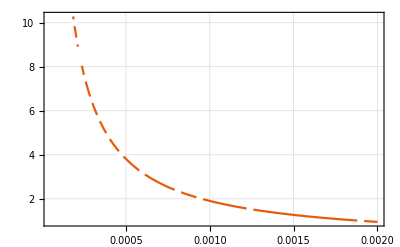

```mathematica
Show[Plot[,{x,50*^-6,2*^-3}],ListPlot[data,PlotStyle->White]]
```